```mathematica
T[{t_,β_}]:=Mod[π+ArcTan[(Sin[t]*Sqrt[1-β^2])/(Cos[t]+β)],π];
U[{t_,β_}]:=(Sin[t]*Sqrt[1-β^2])/(Cos[t]+β);
Manipulate[Plot[T[θ,β],{β,-1,1}, PlotRange->{{-1.5,1.5},{0,π}}],{θ,0,π}]
```

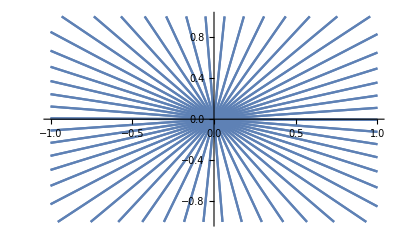

```mathematica
Plot[Map[Tan,2π*(Range[0,1,1/54]-0.001)]*x,{x,-1,1}, PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
Manipulate[Plot[Apply[U,Outer[{#1,#2}&,2π*(Range[0,1,1/54]-0.001),{β}],{1}]*x,{x,-1,1}, PlotRange->{{-1,1},{-1,1}}],{β,0,1,0.05}]
```

```mathematica
Manipulate[Plot[Sqrt[μ^2+α^2]+Sqrt[μ^2+(x-α)^2],{x,0,10},PlotRange->{{0,10},{0,30}}],{μ,0,10},{α,0,10}]
```